```mathematica
pivot[iStar_,jStar_,tableau_]:=(
kk=Dimensions[tableau][[1]];
nn=Dimensions[tableau][[2]];
newTableau=tableau;
newTableau[[1,jStar]]=tableau[[iStar,nn]];
newTableau[[iStar,nn]]=tableau[[1,jStar]];
For[ii=2,ii≤kk,ii++,
For[jj=1,jj<nn,jj++,
{
If[ii==iStar&&jj==jStar,newTableau[[ii,jj]]=1/tableau[[iStar,jStar]]],
If[ii==iStar&&jj≠jStar,newTableau[[ii,jj]]=-tableau[[ii,jj]]/tableau[[iStar,jStar]]],
If[ii≠iStar&&jj==jStar,newTableau[[ii,jj]]=tableau[[ii,jj]]/tableau[[iStar,jStar]]],
If[ii≠iStar&&jj≠jStar,newTableau[[ii,jj]]=tableau[[ii,jj]]-tableau[[iStar,jj]]tableau[[ii,jStar]]/tableau[[iStar,jStar]]] 
}
]
];
Return[newTableau];
)
```

```mathematica
(* max z(x,y) = 17x1 + 11x2 - 9
	g1(x1,x2) = 2x1 + x2 ≤ 32 = b1
   g2(x1,x2) = x1 + x2 ≤ 20 = b2
 g3(x1,x2) = x1 + 2x2 ≤38 = b3
	x≥0
*)

(* Part 1 *)
(* Graph the feasible space *)
Clear[x1,x2]
z[x1_,x2_]:=17x1+11x2-9
g1[x1_,x2_]:=2x1+x2
g2[x1_,x2_]:=x1+x2
g3[x1_,x2_]:=x1+2x2
b1=32;
b2=20;
b3=38;
g1[x1_]:=x2/.Solve[g1[x1,x2]==b1,{x2}][[1,1]]
g2[x1_]:=x2/.Solve[g2[x1,x2]==b2,{x2}][[1,1]]
g3[x1_]:=x2/.Solve[g3[x1,x2]==b3,{x2}][[1,1]]
Plot[{g1[x],g2[x],g3[x]},{x,-10,50},AspectRatio->Automatic,PlotRange->{-10,40},PlotLegends -> "Expressions"]
```

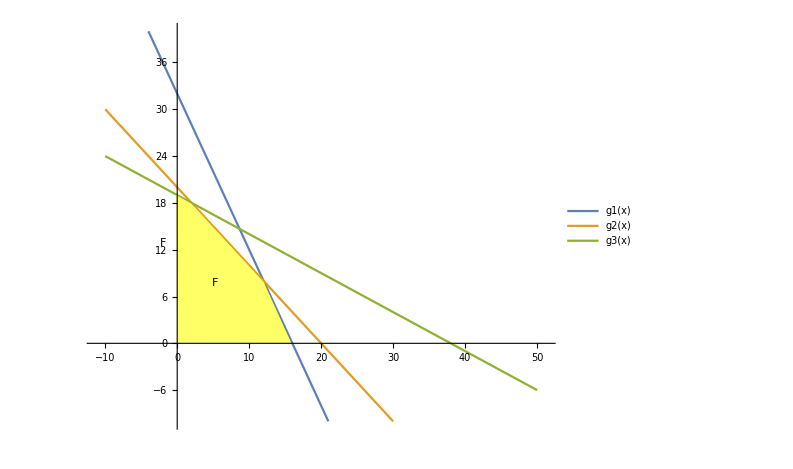

```mathematica
(* Part 2 *)
u=x1/.Solve[g2[x1,x2]==20&&x2==0][[1,1]];
v=x2/.Solve[g2[x1,x2]==20&&x2==0][[1,2]];
b1max = g1[u,v]
```

40

```mathematica
u=x1/.Solve[g2[x1,x2]==20&&g3[x1,x2]==38][[1,1]];
v=x2/.Solve[g2[x1,x2]==20&&g3[x1,x2]==38][[1,2]];
b1min = g1[u,v]
```

22

```mathematica
(* b1:
MIN = 22
MAX = 40
*)
```

```mathematica
u=x1/.Solve[g1[x1,x2]==32&&g3[x1,x2]==38][[1,1]];
v=x2/.Solve[g1[x1,x2]==32&&g3[x1,x2]==38][[1,2]];
b2max = g2[u,v]
```

70/3

```mathematica
u=x1/.Solve[g3[x1,x2]==38&&x1==0][[1,1]];
v=x2/.Solve[g3[x1,x2]==38&&x1==0][[1,2]];
b2min = g2[u,v]
```

19

```mathematica
(* b2:
MIN = 19
MAX = 70/3
*)
```

```mathematica
u=x1/.Solve[g2[x1,x2]==20&&x1==0][[1,1]];
v=x2/.Solve[g2[x1,x2]==20&&x1==0][[1,2]];
b3max = g3[u,v]
```

40

```mathematica
u=x1/.Solve[g1[x1,x2]==32&&g2[x1,x2]==20][[1,1]];
v=x2/.Solve[g1[x1,x2]==32&&g2[x1,x2]==20][[1,2]];
b3min = g3[u,v]
```

28

```mathematica
(* b3:
MIN = 28
MAX = 40
*)
```

```mathematica
(* Part 3 *)
```

```mathematica
b1=32;
b2=20;
b3=38;
db1=0;
db2=0;
db3=0;
m0={" ","x1","x2",1," "};
m1={"y1",-2,-1,(b1+db1),"s1"}; (* baseline b1 = 32 (db1=0) *)
m2={"y2",-1,-1,(b2+db2),"s2"}; (* baseline b2 = 20 (db2=0) *)
m3={"y3",-1,-2,(b3+db3),"s3"};(* baseline b3 = 38 (db3=0)*)
mobj={-1,-17,-11,9,"-z→min"};
mdualSlack={"",-"v1",-"v2","w→max" ,""};
a={m0,m1,m2,m3,mobj,mdualSlack};
Print["baseline initial = ",MatrixForm[a]];
```

baseline initial = (  | x1 | x2 | 1 |  
y1 | -2 | -1 | 32 | s1
y2 | -1 | -1 | 20 | s2
y3 | -1 | -2 | 38 | s3
-1 | -17 | -11 | 9 | -z→min
 | -v1 | -v2 | w→max | )

```mathematica
b=pivot[2,2,a];
Print["b = ",MatrixForm[b]];
```

b = (  | s1 | x2 | 1 |  
y1/2 | -1/2 | -1/2 | 16 | x1
-y1/2+y2 | 1/2 | -1/2 | 4 | s2
-y1/2+y3 | 1/2 | -3/2 | 22 | s3
-1-(17 y1)/2 | 17/2 | -5/2 | -263 | -z→min
-(v1 y1)/2 | v1/2 | v1/2-v2 | -16 v1+w→max | )

```mathematica
c=pivot[3,3,b];
Print["c = ",MatrixForm[c]];
```

c = (  | s1 | s2 | 1 |  
y1-y2 | -1 | 1 | 12 | x1
-2 (y1/2-y2) | 1 | -2 | 8 | x2
-y1/2-3 (-y1/2+y2)+y3 | -1 | 3 | 10 | s3
-1-(17 y1)/2-5 (-y1/2+y2) | 6 | 5 | -283 | -z→min
-(v1 y1)/2+2 (v1/2-v2) (-y1/2+y2) | v1-v2 | -2 (v1/2-v2) | -16 v1+8 (v1/2-v2)+w→max | )

```mathematica
(* primary (row) basic solution *)
xStarBase={12,8};
zStarBase=283;
(* dual (col) basic solution does not change in the range of db considered *)
yStar={6,5,0};
wStar=283;
(* to avoid long variable names define the following abbreviations *)
y1 = yStar[[1]];
y2 = yStar[[2]];
y3 = yStar[[3]];
```

```mathematica
m0={" ","y1","y2","y3 "," "};
m1={"x1",-2,-1,(b1+db1),"s1"}; (* baseline b1 = 32 (db1=0) *)
m2={"x2",-1,-1,(b2+db2),"s2"}; (* baseline b2 = 20 (db2=0) *)
m3={"-1",-1,-2,(b3+db3),"s3"};(* baseline b3 = 38 (db3=0)*)
mobj={-1,-17,-11,9,"-z→min"};
mdualSlack={"",-"v1",-"v2","w→max" ,""};
a={m0,m1,m2,m3,mobj,mdualSlack};
Print["baseline initial = ",MatrixForm[a]];
```

baseline initial = (  | y1 | y2 | y3  |  
x1 | -2 | -1 | 32 | s1
x2 | -1 | -1 | 20 | s2
-1 | -1 | -2 | 38 | s3
-1 | -17 | -11 | 9 | -z→min
 | -v1 | -v2 | w→max | )

```mathematica
m0={"","y1","y2","y3",1,""};
m1={"x1",2,1,1,-17,"v1"};
m2={"x2",1,1,2,-11,"v2"};
mobj={-1,32,20,38,-9,"w→max"};
mbottom={"",-"s1",-"s2",-"s3","-z→min",""};
aaa={m0,m1,m2,mobj,mbottom};
MatrixForm[aaa]
```

( | y1 | y2 | y3 | 1 | 
x1 | 2 | 1 | 1 | -17 | v1
x2 | 1 | 1 | 2 | -11 | v2
-1 | 32 | 20 | 38 | -9 | w→max
 | -s1 | -s2 | -s3 | -z→min | )

```mathematica
d=pivot[2,2,aaa];
Print["d = ",MatrixForm[d]];
```

d = ( | v1 | y2 | y3 | 1 | 
-x1/2 | 1/2 | -1/2 | -1/2 | 17/2 | y1
-x1/2+x2 | 1/2 | 1/2 | 3/2 | -5/2 | v2
-1-16 x1 | 16 | 4 | 22 | 263 | w→max
+(s1 x1)/2 | -s1/2 | s1/2-s2 | s1/2-s3 | -(17 s1)/2+-z→min | )

```mathematica
e=pivot[3,3,d];
Print["e = ",MatrixForm[e]];
```

e = ( | v1 | v2 | y3 | 1 | 
-x1+x2 | 1 | -1 | 1 | 6 | y1
2 (x1/2-x2) | -1 | 2 | -3 | 5 | y2
-1-16 x1-8 (-x1/2+x2) | 12 | 8 | 10 | 283 | w→max
+(s1 x1)/2-2 (s1/2-s2) (-x1/2+x2) | -s1+s2 | 2 (s1/2-s2) | s1/2-3 (s1/2-s2)-s3 | -(17 s1)/2+5 (s1/2-s2)+-z→min | )

```mathematica
(* We can see that solving LP in row tableau or column tableau 
by the simplex algorithm would lead to the exactly same anwser *)
```

```mathematica
(* Part 4 *)
```

```mathematica
Clear[z,zStar,b1,b2,b3]
x1Star[b1_,b2_]:=x1/.Solve[g1[x1,x2]==b1&&g2[x1,x2]==b2,{x1,x2}][[1,1]]
x2Star[b1_,b2_]:=x2/.Solve[g1[x1,x2]==b1&&g2[x1,x2]==b2,{x1,x2}][[1,2]]
z[x1_,x2_]:=17x1+11x2-9
zStar[b1_,b2_]:=z[x1Star[b1,b2],x2Star[b1,b2]]
Print["zStar[b1,b2] = ",Simplify[zStar[b1,b2]]]
dzdb1=D[zStar[b1,b2],{b1,1}]
dzdb2=D[zStar[b1,b2],{b2,1}]
dzdb3=D[zStar[b1,b2],{b3,1}]
y1==dzdb1
y2==dzdb2
y3==dzdb3
```

zStar[b1,b2] = -9+6 b1+5 b2

6

5

0

True

True

True

```mathematica
(* Part 5 *)
```

```mathematica
b1=32;
b2=20;
b3=38;
delz={17,11}; 
delg1={2,1};
delg2={1,1};
delg3={1,2};
```

```mathematica
(* a) db=(0 2 0) *)
```

```mathematica
db1=0;
db2=2;
db3=0;
m0={" ","x1","x2",1," "};
m1={"y1",-2,-1,(b1+db1),"s1"}; (* baseline b1 =  32(db1=0) *)
m2={"y2",-1,-1,(b2+db2),"s2"}; (* baseline b2 = 20 (db2=2) *)
m3={"y3",-1,-2,(b3+db3),"s3"};(* baseline b3 = 38 (db3=0)*)
mobj={-1,-17,-11,9,"-z→min"};
mdualSlack={"",-"v1",-"v2","w→max" ,""};
a={m0,m1,m2,m3,mobj,mdualSlack};
Print["db=(0,2,0) initial = ",MatrixForm[a]];
```

db=(0,2,0) initial = (  | x1 | x2 | 1 |  
y1 | -2 | -1 | 32 | s1
y2 | -1 | -1 | 22 | s2
y3 | -1 | -2 | 38 | s3
-1 | -17 | -11 | 9 | -z→min
 | -v1 | -v2 | w→max | )

```mathematica
b=pivot[2,2,a];
Print["b = ",MatrixForm[b]];
```

b = (  | s1 | x2 | 1 |  
y1/2 | -1/2 | -1/2 | 16 | x1
-y1/2+y2 | 1/2 | -1/2 | 6 | s2
-y1/2+y3 | 1/2 | -3/2 | 22 | s3
-1-(17 y1)/2 | 17/2 | -5/2 | -263 | -z→min
-(v1 y1)/2 | v1/2 | v1/2-v2 | -16 v1+w→max | )

```mathematica
c=pivot[3,3,b];
Print["db=(0,2,0) optimal = ",MatrixForm[c]];
```

db=(0,2,0) optimal = (  | s1 | s2 | 1 |  
y1-y2 | -1 | 1 | 10 | x1
-2 (y1/2-y2) | 1 | -2 | 12 | x2
-y1/2-3 (-y1/2+y2)+y3 | -1 | 3 | 4 | s3
-1-(17 y1)/2-5 (-y1/2+y2) | 6 | 5 | -293 | -z→min
-(v1 y1)/2+2 (v1/2-v2) (-y1/2+y2) | v1-v2 | -2 (v1/2-v2) | -16 v1+12 (v1/2-v2)+w→max | )

```mathematica
xStarNew ={10,12};
zStarNew=293
dx=xStarNew-xStarBase
dz = zStarNew-zStarBase
dz==delz.dx==(y1 delg1+y2 delg2+y3 delg3).dx==y1(delg1.dx)+y2(delg2.dx)+y3(delg3.dx)==y1 db1+y2 db2+y3 db3
```

293

{-2,4}

10

True

```mathematica
(* b) db=(3 0 0) *)
```

```mathematica
db1=3;
db2=0;
db3=0;
m0={" ","x1","x2",1," "};
m1={"y1",-2,-1,(b1+db1),"s1"}; (* baseline b1 =  32(db1=3) *)
m2={"y2",-1,-1,(b2+db2),"s2"}; (* baseline b2 = 20 (db2=0) *)
m3={"y3",-1,-2,(b3+db3),"s3"};(* baseline b3 = 38 (db3=0)*)
mobj={-1,-17,-11,9,"-z→min"};
mdualSlack={"",-"v1",-"v2","w→max" ,""};
a={m0,m1,m2,m3,mobj,mdualSlack};
Print["db=(3,0,0) initial = ",MatrixForm[a]];
```

db=(3,0,0) initial = (  | x1 | x2 | 1 |  
y1 | -2 | -1 | 35 | s1
y2 | -1 | -1 | 20 | s2
y3 | -1 | -2 | 38 | s3
-1 | -17 | -11 | 9 | -z→min
 | -v1 | -v2 | w→max | )

```mathematica
b=pivot[2,2,a];
Print["b = ",MatrixForm[b]];
```

b = (  | s1 | x2 | 1 |  
y1/2 | -1/2 | -1/2 | 35/2 | x1
-y1/2+y2 | 1/2 | -1/2 | 5/2 | s2
-y1/2+y3 | 1/2 | -3/2 | 41/2 | s3
-1-(17 y1)/2 | 17/2 | -5/2 | -577/2 | -z→min
-(v1 y1)/2 | v1/2 | v1/2-v2 | -(35 v1)/2+w→max | )

```mathematica
c=pivot[3,3,b];
Print["db=(3,0,0) optimal = ",MatrixForm[c]];
```

db=(3,0,0) optimal = (  | s1 | s2 | 1 |  
y1-y2 | -1 | 1 | 15 | x1
-2 (y1/2-y2) | 1 | -2 | 5 | x2
-y1/2-3 (-y1/2+y2)+y3 | -1 | 3 | 13 | s3
-1-(17 y1)/2-5 (-y1/2+y2) | 6 | 5 | -301 | -z→min
-(v1 y1)/2+2 (v1/2-v2) (-y1/2+y2) | v1-v2 | -2 (v1/2-v2) | -(35 v1)/2+5 (v1/2-v2)+w→max | )

```mathematica
xStarNew ={15,5};
zStarNew=301
dx=xStarNew-xStarBase
dz = zStarNew-zStarBase
dz==delz.dx==(y1 delg1+y2 delg2+y3 delg3).dx==y1(delg1.dx)+y2(delg2.dx)+y3(delg3.dx)==y1 db1+y2 db2+y3 db3
```

301

{3,-3}

18

True

```mathematica
(* c) db=(3 2 0) *)
```

```mathematica
db1=3;
db2=2;
db3=0;
m0={" ","x1","x2",1," "};
m1={"y1",-2,-1,(b1+db1),"s1"}; (* baseline b1 =  32(db1=3) *)
m2={"y2",-1,-1,(b2+db2),"s2"}; (* baseline b2 = 20 (db2=2) *)
m3={"y3",-1,-2,(b3+db3),"s3"};(* baseline b3 = 38 (db3=0)*)
mobj={-1,-17,-11,9,"-z→min"};
mdualSlack={"",-"v1",-"v2","w→max" ,""};
a={m0,m1,m2,m3,mobj,mdualSlack};
Print["db=(3,2,0) initial = ",MatrixForm[a]];
```

db=(3,2,0) initial = (  | x1 | x2 | 1 |  
y1 | -2 | -1 | 35 | s1
y2 | -1 | -1 | 22 | s2
y3 | -1 | -2 | 38 | s3
-1 | -17 | -11 | 9 | -z→min
 | -v1 | -v2 | w→max | )

```mathematica
b=pivot[2,2,a];
Print["b = ",MatrixForm[b]];
```

b = (  | s1 | x2 | 1 |  
y1/2 | -1/2 | -1/2 | 35/2 | x1
-y1/2+y2 | 1/2 | -1/2 | 9/2 | s2
-y1/2+y3 | 1/2 | -3/2 | 41/2 | s3
-1-(17 y1)/2 | 17/2 | -5/2 | -577/2 | -z→min
-(v1 y1)/2 | v1/2 | v1/2-v2 | -(35 v1)/2+w→max | )

```mathematica
c=pivot[3,3,b];
Print["db=(3,2,0) optimal = ",MatrixForm[c]];
```

db=(3,2,0) optimal = (  | s1 | s2 | 1 |  
y1-y2 | -1 | 1 | 13 | x1
-2 (y1/2-y2) | 1 | -2 | 9 | x2
-y1/2-3 (-y1/2+y2)+y3 | -1 | 3 | 7 | s3
-1-(17 y1)/2-5 (-y1/2+y2) | 6 | 5 | -311 | -z→min
-(v1 y1)/2+2 (v1/2-v2) (-y1/2+y2) | v1-v2 | -2 (v1/2-v2) | -(35 v1)/2+9 (v1/2-v2)+w→max | )

```mathematica
xStarNew ={13,9};
zStarNew=311
dx=xStarNew-xStarBase
dz = zStarNew-zStarBase
dz==delz.dx==(y1 delg1+y2 delg2+y3 delg3).dx==y1(delg1.dx)+y2(delg2.dx)+y3(delg3.dx)==y1 db1+y2 db2+y3 db3
```

311

{1,1}

28

True

```mathematica
(* d) db=(3 -2 0) *)
```

```mathematica
db1=3;
db2=-2;
db3=0;
m0={" ","x1","x2",1," "};
m1={"y1",-2,-1,(b1+db1),"s1"}; (* baseline b1 =  32(db1=3) *)
m2={"y2",-1,-1,(b2+db2),"s2"}; (* baseline b2 = 20 (db2=-2) *)
m3={"y3",-1,-2,(b3+db3),"s3"};(* baseline b3 = 38 (db3=0)*)
mobj={-1,-17,-11,9,"-z→min"};
mdualSlack={"",-"v1",-"v2","w→max" ,""};
a={m0,m1,m2,m3,mobj,mdualSlack};
Print["db=(3,-2,0) initial = ",MatrixForm[a]];
```

db=(3,-2,0) initial = (  | x1 | x2 | 1 |  
y1 | -2 | -1 | 35 | s1
y2 | -1 | -1 | 18 | s2
y3 | -1 | -2 | 38 | s3
-1 | -17 | -11 | 9 | -z→min
 | -v1 | -v2 | w→max | )

```mathematica
b=pivot[2,2,a];
Print["b = ",MatrixForm[b]];
```

b = (  | s1 | x2 | 1 |  
y1/2 | -1/2 | -1/2 | 35/2 | x1
-y1/2+y2 | 1/2 | -1/2 | 1/2 | s2
-y1/2+y3 | 1/2 | -3/2 | 41/2 | s3
-1-(17 y1)/2 | 17/2 | -5/2 | -577/2 | -z→min
-(v1 y1)/2 | v1/2 | v1/2-v2 | -(35 v1)/2+w→max | )

```mathematica
c=pivot[3,3,b];
Print["db=(3,-2,0) optimal = ",MatrixForm[c]];
```

db=(3,-2,0) optimal = (  | s1 | s2 | 1 |  
y1-y2 | -1 | 1 | 17 | x1
-2 (y1/2-y2) | 1 | -2 | 1 | x2
-y1/2-3 (-y1/2+y2)+y3 | -1 | 3 | 19 | s3
-1-(17 y1)/2-5 (-y1/2+y2) | 6 | 5 | -291 | -z→min
-(v1 y1)/2+2 (v1/2-v2) (-y1/2+y2) | v1-v2 | -2 (v1/2-v2) | -17 v1-v2+w→max | )

```mathematica
xStarNew ={17,1};
zStarNew=291
dx=xStarNew-xStarBase
dz = zStarNew-zStarBase
dz==delz.dx==(y1 delg1+y2 delg2+y3 delg3).dx==y1(delg1.dx)+y2(delg2.dx)+y3(delg3.dx)==y1 db1+y2 db2+y3 db3
```

291

{5,-7}

8

True